```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/alexander/Documents/Github/Numerical-Recipe/Lab 3

```mathematica
data=Import["Lab3size16.dat","Data"];
```

```mathematica
points=Table[{i[[1]],i[[2]]},{i,data}]
```

{{1.,0.156104},{1.025,0.175345},{1.05,0.196813},{1.075,0.221598},{1.1,0.242729},{1.125,0.275117},{1.15,0.310608},{1.175,0.331493},{1.2,0.365082},{1.225,0.413196},{1.25,0.463797},{1.275,0.51056},{1.3,0.549345},{1.325,0.61968},{1.35,0.699112},{1.375,0.783167},{1.4,0.891265},{1.425,1.0149},{1.45,1.13303},{1.475,1.38242},{1.5,1.48633},{1.525,1.71626},{1.55,1.65397},{1.575,1.54723},{1.6,1.41826},{1.625,1.22928},{1.65,1.0907},{1.675,0.956303},{1.7,0.898246},{1.725,0.786874},{1.75,0.727759},{1.775,0.67829},{1.8,0.644363},{1.825,0.600955},{1.85,0.579953},{1.875,0.540076},{1.9,0.518087},{1.925,0.495842},{1.95,0.479033},{1.975,0.466376},{2.,0.437014}}

```mathematica
points={{1.,0.177885},{1.05,0.214782},{1.075,0.236841},{1.1,0.260437},{1.125,0.295162},{1.15,0.318973},{1.175,0.344572},{1.2,0.387554},{1.225,0.422251},{1.25,0.47106},{1.275,0.543885},{1.3,0.573003},{1.325,0.634151},{1.35,0.67937},{1.375,0.765758},{1.4,0.867803},{1.425,1.048271},{1.45,1.093132},{1.475,1.151321},{1.5,1.723231},{1.525,1.803593},{1.55,1.801108},{1.575,1.720295},{1.6,1.368891},{1.625,1.19475},{1.65,1.047947},{1.675,0.93068},{1.7,0.821856},{1.725,0.764837},{1.75,0.702322},{1.775,0.676903},{1.8,0.623887},{1.825,0.607346},{1.85,0.57327},{1.875,0.541916},{1.9,0.525707},{1.925,0.497692},{1.95,0.478251},{1.975,0.457467},{2.,0.441593}}
```

{{1.,0.177885},{1.05,0.214782},{1.075,0.236841},{1.1,0.260437},{1.125,0.295162},{1.15,0.318973},{1.175,0.344572},{1.2,0.387554},{1.225,0.422251},{1.25,0.47106},{1.275,0.543885},{1.3,0.573003},{1.325,0.634151},{1.35,0.67937},{1.375,0.765758},{1.4,0.867803},{1.425,1.04827},{1.45,1.09313},{1.475,1.15132},{1.5,1.72323},{1.525,1.80359},{1.55,1.80111},{1.575,1.7203},{1.6,1.36889},{1.625,1.19475},{1.65,1.04795},{1.675,0.93068},{1.7,0.821856},{1.725,0.764837},{1.75,0.702322},{1.775,0.676903},{1.8,0.623887},{1.825,0.607346},{1.85,0.57327},{1.875,0.541916},{1.9,0.525707},{1.925,0.497692},{1.95,0.478251},{1.975,0.457467},{2.,0.441593}}

```mathematica
fit=NonlinearModelFit[points,(a0+a1 x+a2 x^2+a3 x^3+a4 x^4)/(b0+b1 x+b2 x^2+b3 x^3+b4 x^4),{a0,a1,a2,a3,a4,b0,b1,b2,b3,b4},x]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[(«6»+13.735 x^4)/(«6»+75.305 x^4)]

```mathematica
a=Normal[fit]
```

(47.985-134.969 x+146.954 x^2-72.7871 x^3+13.735 x^4)/(354.125-953.659 x+969.037 x^2-440.049 x^3+75.305 x^4)

```mathematica
(47.984979043772704-134.96859054717058 x+146.95410370549533 x^2-72.78713431452175 x^3+13.73498544007537 x^4)/(354.12532409527125-953.659414681753 x+969.036859484632 x^2-440.0491068903782 x^3+75.30500514977594 x^4)
```

(17.0971-49.9508 x+61.9666 x^2-36.0571 x^3+7.96189 x^4)/(363.455-962.525 x+968.738 x^2-438.628 x^3+75.2945 x^4)

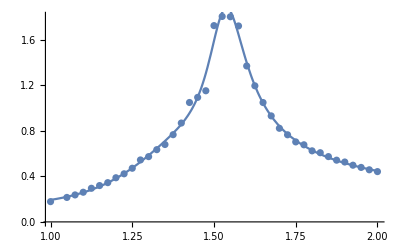

```mathematica
Show[ListPlot[points],Plot[a,{x,1,2}]]
```

```mathematica
b=D[a,x]
```

-(((-953.659+1938.07 x-1320.15 x^2+301.22 x^3) (47.985-134.969 x+146.954 x^2-72.7871 x^3+13.735 x^4))/(354.125-953.659 x+969.037 x^2-440.049 x^3+75.305 x^4)^2)+(-134.969+293.908 x-218.361 x^2+54.9399 x^3)/(354.125-953.659 x+969.037 x^2-440.049 x^3+75.305 x^4)

```mathematica
NSolve[b==0,x]
```

{{x→1.09554×10^14},{x→1.56891-0.187347 ⅈ},{x→1.56891+0.187347 ⅈ},{x→1.53836},{x→1.41308-0.0950638 ⅈ},{x→1.41308+0.0950638 ⅈ},{x→0.469215}}